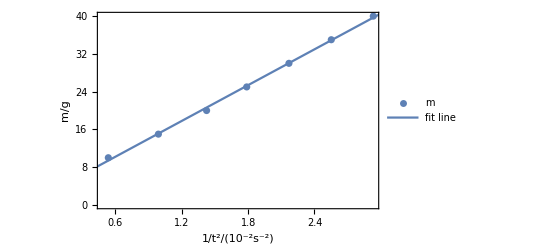

```mathematica
data={{0.535,10},{0.988,15},{1.424,20},{1.787,25},{2.169,30},{2.552,35},{2.932,40}};
f=Fit[data,{1,x},x];
l=ListPlot[data,Frame->True,PlotLegends->{"m"}];
p=Plot[f,{x,0,3},Frame->True,PlotLegends->{"fit line"}];
Show[l,p,AxesLabel->{"1/t^2/(10^-2s^-2)","m/g"}]
```